1

1

3

1

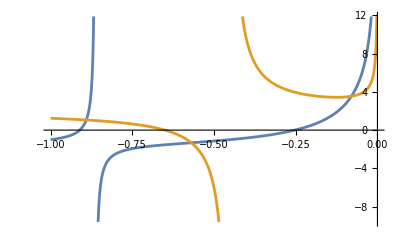

；^2 Null^3

{{En→-0.910757},{En→-0.252509}}

{{En→-0.650311}}

```mathematica
m = 1
V0=1
a = 3
hbar = 1(*自然单位制*)


k1[En_]:=Sqrt[2 m (En+V0)/hbar^2];
k2[En_]:=Sqrt[-2 m En/hbar^2];

(*处理了求解En的方程并绘图方便寻找合适的初值虽然之后并没有用到*)
f[En_]:=(k1[En]/k2[En]) Tan[k1[En] a]-1
g[En_]:=(k1[En]/k2[En]) Cot[k1[En] a]+1
Plot[{f[En],g[En]},{En,-1,0}]


even[En_]:=k1[En] Tan[k1[En] a]==k2[En]；
odd[En_]:=k1[En] Cot[k1[En] a]==-k2[En]；


(*为了找实根抄的一段函数也没有用到myFindRoot[eqn_,range_,opts___]:=Module[{sol},sol=Quiet@FindRoot[eqn,range,opts];
If[Abs[(eqn/. Equal->Subtract)/. sol]<=1.*^-8,sol,{}]];*)
evenE=Table[FindRoot[even[En],{En,n-1}
],{n,{0.1,0.75}}];
oddE=Table[FindRoot[odd[En],{En,n-1}
],{n,{0.4}}];
evenE
oddE
```

```mathematica
(*波函数*)evenWaveFunction[En_,x_]:=Piecewise[{{Cos[k1[En] x],Abs[x]<a},{Cos[k1[En] a] Exp[-k2[En] (Abs[x]-a)],Abs[x]>=a}}];

oddWaveFunction[En_,x_]:=Piecewise[{{Sin[k1[En] x],Abs[x]<a},{Sign[x] Sin[k1[En] a] Exp[-k2[En] (Abs[x]-a)],Abs[x]>=a}}];

(*归一化因子,哈哈它算不出来，我自己手算吧
normalize[wave_,En_]:=1/Sqrt[NIntegrate[wave[En,x]^2,{x,-Infinity,Infinity}]];*)
evenNormalize[En_]:=1/Sqrt[a+Sin[2k1[En] a]/(2k1[En])+Cos[k1[En] a]^2/k2[En]];
oddNormalize[En_]:=1/Sqrt[a-Sin[2k1[En] a]/(2k1[En])+Cos[k1[En] a]^2/k2[En]];
```

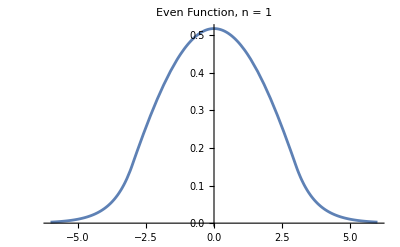
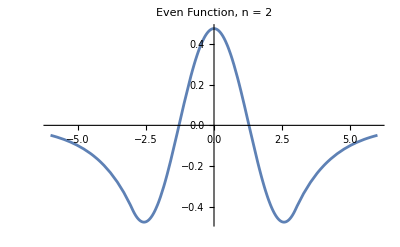

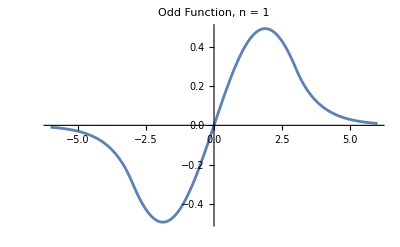

```mathematica
(*图*)evenPlots=Table[Plot[evenNormalize[En]*evenWaveFunction[En,x]/. evenE[[n]],{x,-2 a,2 a},PlotRange->All,PlotLabel->"Even Function, n = "<>ToString[n]],{n,1,Length[evenE]}]

(*奇函数波函数图*)
oddPlots=Table[Plot[oddNormalize[En]*oddWaveFunction[En,x]/. oddE[[n]],{x,-2 a,2 a},PlotRange->All,PlotLabel->"Odd Function, n = "<>ToString[n]],{n,1,Length[oddE]}]

(*好感动终于画出来了*)
```